## Harvest model with Type III response - multiplicative noise

## Setup and Universal Parameters

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fold_harvest/figures"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* get packages for user-defined functions *)
Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/mma_functions/ews_spec.wl"];

Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/mma_functions/ews_std.wl"];
```

```mathematica
(* Universal simulation parameters *)
dt=1; (* time step for stochastic simulation *)
dt2 = 1; (* time separation for indicator calculation - increase to speed up computation *)
tmax=1000 ; (* max time in simulation *)
numSims=5; (* number of realisations to average over *)

(* options for EWS calculation *)
detrendOp=1; (* 1 for yes, 0 for no *)
bandWidth=0.2; (* for Gaussian filtering (as a percentage) *)
rollWindow=0.25;(* for indicator calculation *)
toffset=0; (* time before bifurcation point to stop evaluating EWS *)

(* hamming window size and length *)
hamLength=10; 
hamOffset=5; 


(* lag autocorrelation *)
numComps=tmax/dt+1; (* number of components in simulation *)
tauVals={1,2};

(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,50,20,20};  (* image padding *)
indexPos=Scaled[{0.065,1.10}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
```

```mathematica
?TBindPlot
```

plot = TBindPlot[data] takes in times-series data and produces a plot with the chosen specifications.
Input vars
data: list of time-series of the form {{t1,x1},{t2,x2},...,{tn,xn}}

Optional arguments (default)
TBxAxes: (False) : choose whether to include x ticks and label
TBlabel: ('' '') : figure label in top left corner
TByLabel: ('' '') : y axes label
TBarrow: (False) : choose whether to include an arrow denoting rolling window
TByRange: (All) : specify a particular range in y values

Output vars
plot: a grid of plots

## Model Analysis

Use bistable harvesting model : dx/dt = rx(1-x/K) - hx^2/(s^2 +x^2)

```mathematica
(* Clear variable names *)
Clear[f,x,r,h,s,k]
$Assumptions={x,r,s,k}∈Reals;
```

```mathematica
(* Dynamic equations *)
f[x_]:=r x(1-x/k) - h x^2/(s^2+x^2);
```

```mathematica
f[x]
```

r x (1-x/k)-(h x^2)/(s^2+x^2)

```mathematica
(* Parameter values *)
r=1;
k=1;
s=0.1;
```

```mathematica
(* Find equilibiria *)
equi=Solve[f[x]==0,x]//Quiet;
```

```mathematica
equi/.{h->0.1}
```

{{x→0.},{x→0.0555458+0.0903572 ⅈ},{x→0.888908+0. ⅈ},{x→0.0555458-0.0903572 ⅈ}}

```mathematica
(* Initial stable equilibrium *)
equiInit=Re[x/.equi[[3]]];

(* Bifurcation point *)
{xbif,hbif}=Re[{x,h}/.Solve[f[x]==0&&f'[x]==0][[3]]]//Quiet
```

{0.478128,0.260437}

```mathematica
(* Eigenvalue at equilibrium point *)
Clear[λ]
λ[a_]=D[f[x],x]/.{x->equiInit};
```

```mathematica
(* Phase portrait, hval control parameter *)
Manipulate[
Plot[f[x]/.{r->rval,h->hval,s->sval},{x,0,1},
PlotRange->{-0.2,0.2},
AxesLabel->{"x","f(x)"},
LabelStyle->TMBFS12],
{{rval,1},0.5,1.5},{{hval,0},0,0.4},{{sval,0.1},0.05,0.3}];
```

## Stochastic Simulation

Stochastic model 
dX = rX(1-X/K) -hX^2/(s^2+X^2)

### Key parameters

```mathematica
a1=0.02;(* noise intensity *)
r=1; (* model parameteres *)
s=0.1;
k=1;
hl=0.15; (* min value of control parameter *)
hh=0.28; (* max value of control parameter *)
x0=equiInit/.h->hl; (* initial condition *)
seed=10; (* seed number *)

(* lag autocorrelation *)
numComps=tmax/dt+1;
tauVals={1,2};
```

### Model Dynamics

```mathematica
Clear[f]
f[x_,r_,s_,k_,h_]:=r x(1-x/k)-h x^2/(s^2+x^2);
```

### Stochastic Simulation Setup

```mathematica
(* clear function labels *)
Clear[stochProc,stochSol,stochData]
```

```mathematica
(* evolution of control param - harvesting rate *)
Clear[h,t]
h[t_]:=((hh-hl)/tmax) t +hl
```

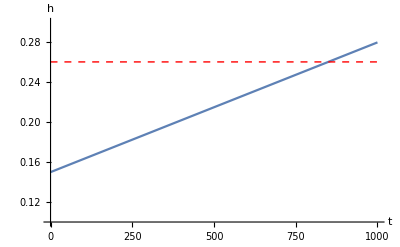

```mathematica
(* Critical time *)
tcrit=t/.Solve[h[t]==hbif,t][[1]];

(* h plot *)
hPlot=Plot[{h[t],hbif},{t,0,tmax},
LabelStyle->14,
AxesLabel->{"t","h"},
PlotStyle->{Automatic,{Dashed,Thick,Red}},
PlotRange->{{0,tmax},{0.1,0.3}}]
```

```mathematica
(* number of components in simulation *)
nComps=Floor[tmax/dt]+1;
```

```mathematica
(* array for output time-series *)
t=Range[0,tmax,dt];
xr=ConstantArray[0,{numSims,nComps}]; (* x values with noise to r *)
xk=ConstantArray[0,{numSims,nComps}]; (* x values with noise to k *)
xs=ConstantArray[0,{numSims,nComps}]; (* x values with noise to s *)
xAdd=ConstantArray[0,{numSims,nComps}]; (* x values with additive noise to state *)
xMulti=ConstantArray[0,{numSims,nComps}]; (* x values with mutliplicative noise proportional to state *)
```

```mathematica
(* intitial condition *)
xr[[;;,1]]=x0;
xk[[;;,1]]=x0;
xs[[;;,1]]=x0;
xAdd[[;;,1]]=x0;
xMulti[[;;,1]]=x0;
```

### Noise set up

```mathematica
(* noise amplitudes for parameters *)
rAmp=0.1; (* as proportion of parameter *)
kAmp=0.05;
sAmp=0.05;
addAmp=a1;
multiAmp=a1;
```

```mathematica
(* noisy parameter values *)
rNoise=r+rAmp*RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
kNoise=k+kAmp*RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
sNoise=s+sAmp*RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
```

```mathematica
(* multiplicative state noise values *)
multiStateNoise=Sqrt[dt]*multiAmp*RandomVariate[NormalDistribution[0,1],{numSims,nComps}];

(* additive state noise values *)
addStateNoise=Sqrt[dt]*addAmp*RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
```

### Simulations

```mathematica
f[x_,r_,s_,k_,h_]:=r x(1-x/k)-h x^2/(s^2+x^2);
```

#### Noise on r

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
xr[[j,i+1]]=xr[[j,i]]+f[xr[[j,i]],rNoise[[j,i]],s,k,h[t[[i]]]]dt;
(* make sure state variable stays above x=0 *)
If[xr[[j,i+1]]≤0,xr[[j,i+1]]=0];
]
]
```

#### Noise on K

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
xk[[j,i+1]]=xk[[j,i]]+f[xk[[j,i]],r,s,kNoise[[j,i]],h[t[[i]]]]dt;
(* make sure state variable stays above x=0 *)
If[xk[[j,i+1]]≤0,xk[[j,i+1]]=0];
]
]
```

#### Noise on s

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
xs[[j,i+1]]=xs[[j,i]]+f[xs[[j,i]],r,sNoise[[j,i]],k,h[t[[i]]]]dt;
(* make sure state variable stays above x=0 *)
If[xs[[j,i+1]]≤0,xs[[j,i+1]]=0];
]
]
```

#### Additive noise to state

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
xAdd[[j,i+1]]=xAdd[[j,i]]+f[xAdd[[j,i]],r,s,k,h[t[[i]]]]dt +addStateNoise[[j,i]] ;
(* make sure state variable stays above x=0 *)
If[xAdd[[j,i+1]]≤0,xAdd[[j,i+1]]=0];
]
]
```

#### Multiplicative noise to state

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
xMulti[[j,i+1]]=xMulti[[j,i]]+f[xMulti[[j,i]],r,s,k,h[t[[i]]]]dt+xMulti[[j,i]]*multiStateNoise[[j,i]] ;
(* make sure state variable stays above x=0 *)
If[xMulti[[j,i+1]]≤0,xMulti[[j,i+1]]=0];
]
]
```

#### Coarsen time-series for computational speed

```mathematica
tCrs=t[[1;;-1;;Floor[dt2/dt]]];
xrCrs=xr[[;;,1;;-1;;Floor[dt2/dt]]];
xsCrs=xs[[;;,1;;-1;;Floor[dt2/dt]]];
xkCrs=xk[[;;,1;;-1;;Floor[dt2/dt]]];
xAddCrs=xAdd[[;;,1;;-1;;Floor[dt2/dt]]];
xMultiCrs=xMulti[[;;,1;;-1;;Floor[dt2/dt]]];
```

#### Cheeky plot

```mathematica
{ListLinePlot[xrCrs,ImageSize->300,PlotLabel->"Noise in r"],
ListLinePlot[xsCrs,ImageSize->300,PlotLabel->"Noise in s"],
ListLinePlot[xkCrs,ImageSize->300,PlotLabel->"Noise in k"],
ListLinePlot[xAddCrs,ImageSize->300,PlotLabel->"Additive noise"],
ListLinePlot[xMultiCrs,ImageSize->300,PlotLabel->"Noise prop. to state"]};
```

## Traditional EWS

```mathematica
?TBewsCompute
```

{smooth, residuals, varSeries, acSeries, skewSeries} = TBewsCompute[data] takes in non-stationary data and outputs the smoothed data, residuals, and variance and autocorrelation computed over a rolling window.
Input vars
data: nx2 array of time-series data - form {{t1,x1},{t2,x2},...,{tn,xn}}

Optional arguments (default)
RollWindow (0.25): number in (0,1) - proportion of the length of data to use as a rolling window
BandWidth (0.2): integer value - spacing between data points for computing autocorrelation
LagTimes ({1}): list of integers - spacing between data points for computing autocorrelation

Output vars
smooth: time-series of smoothed data
residuals: time-series of residuals
varSeries: time-seires of variance in residuals
acSeries: list of time-series of autocorrelation of resiudals at each lag time
skewSeries: time-series of skewness in residuals

### Compute EWS for time-series

```mathematica
(* work with data only up to bifurcation (tcrit) minus toffset yrs *)
idxCrit=FirstPosition[tCrs,t_/;t≥tcrit-toffset][[1]]-1;
```

```mathematica
tCrs//Dimensions
```

{1001}

```mathematica
xrCrs//Dimensions
```

{5,1001}

```mathematica
Transpose[{tCrs[[1;;idxCrit]],xrCrs[[1,1;;idxCrit]]}];
```

```mathematica
ewsTradR=Table[TBewsCompute[Transpose[{tCrs[[1;;idxCrit]],xrCrs[[i,1;;idxCrit]]}]],{i,1,numSims}]//Transpose;
```

```mathematica
(* EWS data for each noise type *)
ewsTradR=Table[TBewsCompute[Transpose[{tCrs[[1;;idxCrit]],xrCrs[[i,1;;idxCrit]]}]],{i,1,numSims}];
ewsTradS=Table[TBewsCompute[Transpose[{tCrs[[1;;idxCrit]],xsCrs[[i,1;;idxCrit]]}]],{i,1,numSims}];
ewsTradK=Table[TBewsCompute[Transpose[{tCrs[[1;;idxCrit]],xkCrs[[i,1;;idxCrit]]}]],{i,1,numSims}];
ewsTradAdd=Table[TBewsCompute[Transpose[{tCrs[[1;;idxCrit]],xAddCrs[[i,1;;idxCrit]]}]],{i,1,numSims}];
ewsTradMulti=Table[TBewsCompute[Transpose[{tCrs[[1;;idxCrit]],xMultiCrs[[i,1;;idxCrit]]}]],{i,1,numSims}];
```

```mathematica
(* Structure: {smoothdata, resiudals, variance, autocorrelation} *)
ewsTradR//Dimensions
```

{5,5}

### Plot of smoothing

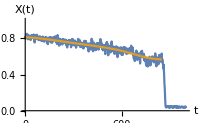

```mathematica
ListPlot[{{tCrs,xrCrs[[1]]}ᵀ,ewsTradR[[1,1]]},
Joined->True,
ImageSize->200,
LabelStyle->14,
AxesLabel->{"t","X(t)"},
PlotRange->{{0,tmax},{0,1}}]
```

### Plot of variances

```mathematica
?TBindPlot
```

plot = TBindPlot[data] takes in times-series data and produces a plot with the chosen specifications.
Input vars
data: list of time-series of the form {{t1,x1},{t2,x2},...,{tn,xn}}

Optional arguments (default)
TBxAxes: (False) : choose whether to include x ticks and label
TBlabel: ('' '') : figure label in top left corner
TByLabel: ('' '') : y axes label
TBarrow: (False) : choose whether to include an arrow denoting rolling window
TByRange: (All) : specify a particular range in y values

Output vars
plot: a grid of plots

```mathematica
windowComps=Floor[rollWindow*idxCrit];
```

```mathematica
(* noise in r *)
plotVarR=TBindPlot[ewsTradR[[;;,3]],TByLabel->"Variance",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"b"];
```

```mathematica
(* noise in k *)
plotVarK=TBindPlot[ewsTradK[[;;,3]],TByLabel->"Variance",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"b"];
```

```mathematica
(* noise in s *)
plotVarS=TBindPlot[ewsTradS[[;;,3]],TByLabel->"Variance",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"b"];
```

```mathematica
(* additive noise *)
plotVarAdd=TBindPlot[ewsTradAdd[[;;,3]],TByLabel->"Variance",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"b"];
```

```mathematica
(* noise proportional to state *)
plotVarMulti=TBindPlot[ewsTradMulti[[;;,3]],TByLabel->"Variance",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"b"];
```

### Plot of autocorrelations at lag-1

```mathematica
?TBindPlot
```

plot = TBindPlot[data] takes in times-series data and produces a plot with the chosen specifications.
Input vars
data: list of time-series of the form {{t1,x1},{t2,x2},...,{tn,xn}}

Optional arguments (default)
TBxAxes: (False) : choose whether to include x ticks and label
TBlabel: ('' '') : figure label in top left corner
TByLabel: ('' '') : y axes label
TBarrow: (False) : choose whether to include an arrow denoting rolling window
TByRange: (All) : specify a particular range in y values

Output vars
plot: a grid of plots

```mathematica
windowComps=Floor[rollWindow*idxCrit];
```

```mathematica
(* noise in r *)
plotAcR=TBindPlot[ewsTradR[[;;,4,1]],TByLabel->"lag-1 AC",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"c"];
```

```mathematica
(* noise in k *)
plotAcK=TBindPlot[ewsTradK[[;;,4,1]],TByLabel->"lag-1 AC",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"c"];
```

```mathematica
(* noise in s *)
plotAcS=TBindPlot[ewsTradS[[;;,4,1]],TByLabel->"lag-1 AC",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"c"];
```

```mathematica
(* additive noise *)
plotAcAdd=TBindPlot[ewsTradAdd[[;;,4,1]],TByLabel->"lag-1 AC",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"c"];
```

```mathematica
(* noise proportional to state *)
plotAcMulti=TBindPlot[ewsTradMulti[[;;,4,1]],TByLabel->"lag-1 AC",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"c"];
```

### Plot of skewness

```mathematica
windowComps=Floor[rollWindow*idxCrit];
```

```mathematica
(* noise in r *)
plotSkewR=TBindPlot[ewsTradR[[;;,5]],TByLabel->"Skewness",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"d"];
```

```mathematica
(* noise in k *)
plotSkewK=TBindPlot[ewsTradK[[;;,5]],TByLabel->"Skewness",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"d"];
```

```mathematica
(* noise in s *)
plotSkewS=TBindPlot[ewsTradS[[;;,5]],TByLabel->"Skewness",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"d"];
```

```mathematica
(* additive noise *)
plotSkewAdd=TBindPlot[ewsTradAdd[[;;,5]],TByLabel->"Skewness",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"d"];
```

```mathematica
(* noise proportional to state *)
plotSkewMulti=TBindPlot[ewsTradMulti[[;;,5]],TByLabel->"Skewness",TBxAxes->False,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"d"];
```

## Power Spectrum EWS

### Compute power spectrum over rolling window with same offset has Hamming windows

```mathematica
?TBewsCompute
```

{smooth, residuals, varSeries, acSeries, skewSeries} = TBewsCompute[data] takes in non-stationary data and outputs the smoothed data, residuals, and variance and autocorrelation computed over a rolling window.
Input vars
data: nx2 array of time-series data - form {{t1,x1},{t2,x2},...,{tn,xn}}

Optional arguments (default)
RollWindow (0.25): number in (0,1) - proportion of the length of data to use as a rolling window
BandWidth (0.2): integer value - spacing between data points for computing autocorrelation
LagTimes ({1}): list of integers - spacing between data points for computing autocorrelation

Output vars
smooth: time-series of smoothed data
residuals: time-series of residuals
varSeries: time-seires of variance in residuals
acSeries: list of time-series of autocorrelation of resiudals at each lag time
skewSeries: time-series of skewness in residuals

```mathematica
(* evaluate power spectrum of residuals in rolling window with the offset the same as hamOffset *)
pSpecSeriesR=Table[MovingMap[TBPowerSpecWelch[{#,dt2,hamLength,hamOffset}]&,ewsTradR[[i,2,;;,2]],{windowComps,Left,hamOffset}],{i,1,numSims}];
pSpecSeriesK=Table[MovingMap[TBPowerSpecWelch[{#,dt2,hamLength,hamOffset}]&,ewsTradK[[i,2,;;,2]],{windowComps,Left,hamOffset}],{i,1,numSims}];
pSpecSeriesS=Table[MovingMap[TBPowerSpecWelch[{#,dt2,hamLength,hamOffset}]&,ewsTradS[[i,2,;;,2]],{windowComps,Left,hamOffset}],{i,1,numSims}];
pSpecSeriesAdd=Table[MovingMap[TBPowerSpecWelch[{#,dt2,hamLength,hamOffset}]&,ewsTradAdd[[i,2,;;,2]],{windowComps,Left,hamOffset}],{i,1,numSims}];
pSpecSeriesMulti=Table[MovingMap[TBPowerSpecWelch[{#,dt2,hamLength,hamOffset}]&,ewsTradMulti[[i,2,;;,2]],{windowComps,Left,hamOffset}],{i,1,numSims}];
```

```mathematica
(* frequncy values of power spectra *)
ωVals=pSpecSeriesR[[1,1,1]];
```

### Plot of individual realisations

```mathematica
pSpecSeriesR//Dimensions
```

{5,128,2,11}

```mathematica
tcrit
```

849.512

```mathematica
(* plot times to use (spaced hamOffset apart) *)
plotTimes=Range[dt2*windowComps,tcrit-50,hamOffset]
```

{212,217,222,227,232,237,242,247,252,257,262,267,272,277,282,287,292,297,302,307,312,317,322,327,332,337,342,347,352,357,362,367,372,377,382,387,392,397,402,407,412,417,422,427,432,437,442,447,452,457,462,467,472,477,482,487,492,497,502,507,512,517,522,527,532,537,542,547,552,557,562,567,572,577,582,587,592,597,602,607,612,617,622,627,632,637,642,647,652,657,662,667,672,677,682,687,692,697,702,707,712,717,722,727,732,737,742,747,752,757,762,767,772,777,782,787,792,797}

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{"TemperatureMap",timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

```mathematica
(* normalise to map to a colour *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
psdSinglePlot=ListLinePlot[Table[Transpose[pSpecSeriesR[[2,tindex]]],{tindex,1,Length[plotTimes]}],
PlotRange->All,
PlotStyle->Thread@{ColorData["TemperatureMap"]/@plotTimesUnit},
LabelStyle->13,
Frame->True,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.7,
FrameLabel->{{"S(ω)",None},{None,None}},
PlotRangeClipping->False,
Epilog->{Text[Style["×10^-3",14],Scaled[{0.065,1.05}]],
Text[Style["d",14,Bold],Scaled[{0.035,0.93}]],
Text[Style["ω",14],Scaled[{1.05,0}]]},
FrameTicks->{{Transpose[{Range[0,5,0.5]*10^(-3),Range[0,5,0.5]}],Automatic},{Automatic,Automatic}},
PlotLegends->Placed[colLegend,Scaled[{0.9,0.55}]]];
```

### Max-frequency component

```mathematica
pSpecSeriesR[[4]]//Dimensions
```

{128,2,11}

```mathematica
(* time values *)
tVals=tCrs[[windowComps+1;;idxCrit;;hamOffset]];
```

```mathematica
Max[pSpecSeriesR[[1,1,2,;;]]]//Dimensions
```

{}

```mathematica
pSpecSeriesR//Dimensions
```

{5,128,2,11}

```mathematica
Max[pSpecSeriesR[[1,1,2,;;]]]
```

0.00106128

```mathematica
specMaxR=Table[Transpose[{tVals,Table[Max[pSpecSeriesR[[i,j,2,;;]]],{j,1,Dimensions[pSpecSeriesR][[2]]}]}],
{i,1,numSims}];
```

```mathematica
(* Subscript[S, max] data *)
specMaxR=Table[Transpose[{tVals,Table[Max[pSpecSeriesR[[i,j,2,;;]]],{j,1,Dimensions[pSpecSeriesR][[2]]}]}],
{i,1,numSims}];
specMaxK=Table[Transpose[{tVals,Table[Max[pSpecSeriesR[[i,j,2,;;]]],{j,1,Dimensions[pSpecSeriesK][[2]]}]}],
{i,1,numSims}];
specMaxS=Table[Transpose[{tVals,Table[Max[pSpecSeriesS[[i,j,2,;;]]],{j,1,Dimensions[pSpecSeriesR][[2]]}]}],
{i,1,numSims}];
specMaxAdd=Table[Transpose[{tVals,Table[Max[pSpecSeriesAdd[[i,j,2,;;]]],{j,1,Dimensions[pSpecSeriesR][[2]]}]}],
{i,1,numSims}];
specMaxMulti=Table[Transpose[{tVals,Table[Max[pSpecSeriesMulti[[i,j,2,;;]]],{j,1,Dimensions[pSpecSeriesR][[2]]}]}],
{i,1,numSims}];
```

### Plots of Smax

```mathematica
(* noise in r *)
plotSmaxR=TBindPlot[specMaxR,TByLabel->"S_max",TBxAxes->True,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"e"];
```

```mathematica
(* noise in K *)
plotSmaxK=TBindPlot[specMaxK,TByLabel->"S_max",TBxAxes->True,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"e"];
```

```mathematica
(* noise in s *)
plotSmaxS=TBindPlot[specMaxS,TByLabel->"S_max",TBxAxes->True,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"e"];
```

```mathematica
(* additive noise *)
plotSmaxAdd=TBindPlot[specMaxAdd,TByLabel->"S_max",TBxAxes->True,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"e"];
```

```mathematica
(* noise proportional to state *)
plotSmaxMulti=TBindPlot[specMaxMulti,TByLabel->"S_max",TBxAxes->True,TBarrow->True,PlotRange->{{0,1000},All},TBlabel->"e"];
```

## Bifurcation diagram

### Specifications

```mathematica
(* Import data *)
rawdata=Import["../bifurcation_data/fold.dat"];

lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{-1,0.5},{-1,1}}; (* plot range *)
(*frLabel={"μ","x"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Info and Setup

Stability representation in .dat file:
	1 - stable node
	2 - unstable node
	3 - stable limit cycle
	4 - unstable limit cycle

```mathematica
legendLine=LineLegend[eqColors,{"Stable node","Unstable node","Stable limit cycle","Unstable limit cycle"}]
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of mu *)
hbifVals=fulldata[[;;,1]];
tbifVals=(hbifVals-hl)*tmax /(hh-hl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
(*nodeSections=Append[nodeSections,Cases[nodeSections[[7]],{_,x_,_,_}/;x<=0.75]];
nodeSections[[7]]=Cases[nodeSections[[7]],{_,x_,_,_}/; x>=0.65] ;*)(* had to seperate out brances for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}];
```

```mathematica
(* Take relevant branches of node sections *)
delList={};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

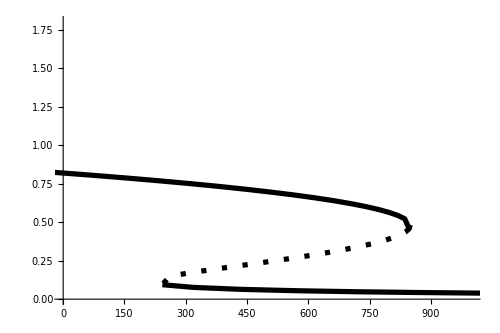

```mathematica
(* Make plot *)
bifPlotNormal=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,1.8}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Output

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.12;
trajVal=0.7;

bifTrajR=Show[{ListLinePlot[xrCrs],bifPlotNormal},
PlotRange->{{0,tmax},{0,1}},
LabelStyle->14,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"X(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
];
```

```mathematica
bifTrajS=Show[{ListLinePlot[xsCrs],bifPlotNormal},
PlotRange->{{0,tmax},{0,1}},
LabelStyle->14,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"X(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
];
```

```mathematica
bifTrajK=Show[{ListLinePlot[xkCrs],bifPlotNormal},
PlotRange->{{0,tmax},{0,1}},
LabelStyle->14,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"X(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
];
```

```mathematica
bifTrajAdd=Show[{ListLinePlot[xAddCrs],bifPlotNormal},
PlotRange->{{0,tmax},{0,1}},
LabelStyle->14,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"X(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
];
```

```mathematica
bifTrajMulti=Show[{ListLinePlot[xMultiCrs],bifPlotNormal},
PlotRange->{{0,tmax},{0,1}},
LabelStyle->14,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"X(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
];
```

## Plots

```mathematica
plotEwsR=Grid[{{bifTrajR},{plotVarR},{plotAcR},{plotSkewR},{plotSmaxR}},Spacings->{-2.5,0}];
```

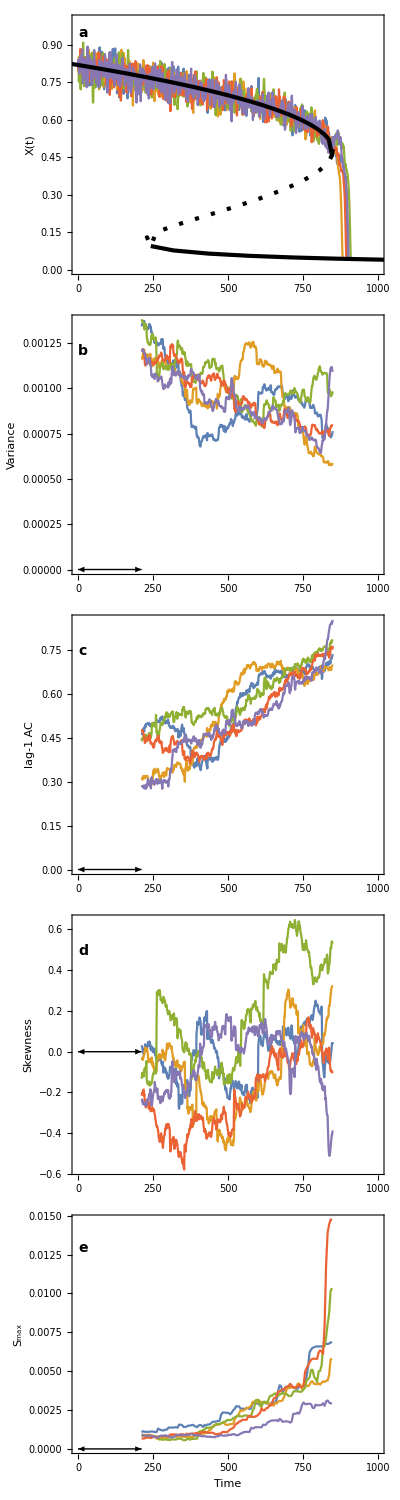

```mathematica
plotEwsK=Grid[{{bifTrajK},{plotVarK},{plotAcK},{plotSkewK},{plotSmaxK}},Spacings->{0,-0.5}]
```

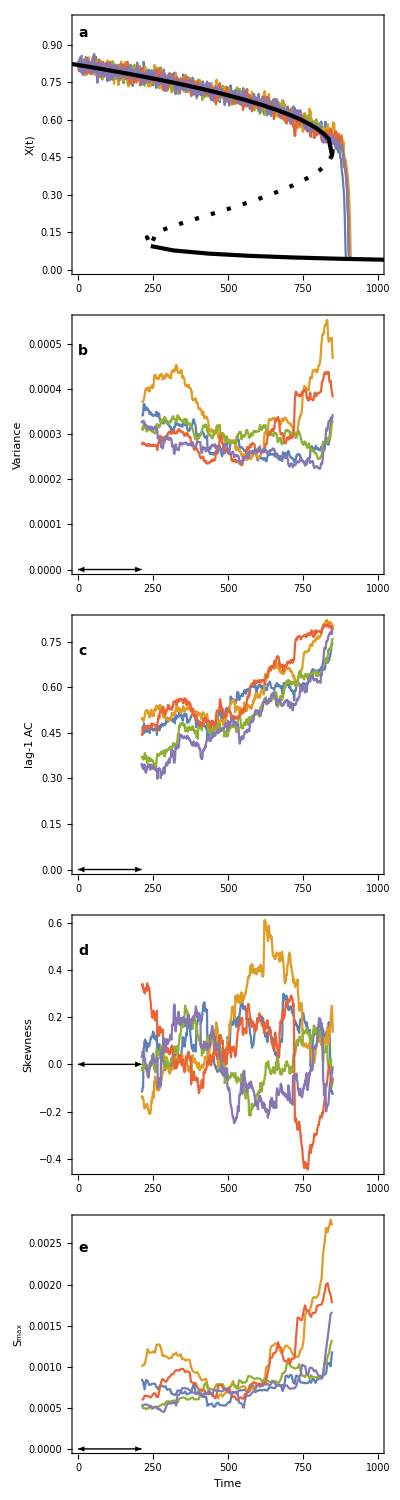

```mathematica
plotEwsMulti=Grid[{{bifTrajMulti},{plotVarMulti},{plotAcMulti},{plotSkewMulti},{plotSmaxMulti}},Spacings->{0,-0.5}]
```